```mathematica
codeLength=22;
NumberToCode=PadLeft[IntegerDigits[#,2],codeLength]&;
CodeToNumber=FromDigits[#,2]&;
```

```mathematica
(*
x,y: variable;
codeLength:编码长度;
generateNum:下一代的种群个体数量;
*)
CrossGenetic[x_,y_,codeLength_,generateNum_]:=Module[{gen1=NumberToCode[x], gen2=NumberToCode[y], start=0, end=0,nextGeneration={},nextGeneration1={},nextGeneration2={}},
({start,end}=Sort[RandomInteger[{2,codeLength-1},2]];nextGeneration1=Join[gen1[[1;;start-1]],gen2[[start;;end]], gen1[[end+1;;-1]]];nextGeneration2=Join[gen2[[1;;start-1]], gen1[[start;;end]], gen2[[end+1;;-1]]];
nextGeneration=Join[nextGeneration,{CodeToNumber[nextGeneration1], CodeToNumber[nextGeneration2]}])&/@Range[generateNum];
nextGeneration
];
```

```mathematica
aberranceGenetic[x_,codeLength_]:=Module[{gen=NumberToCode[x]},
(If[RandomReal[]<0.02,gen[[#]]=1-gen[[#]]])&/@Range[codeLength];
CodeToNumber[gen]
];
```

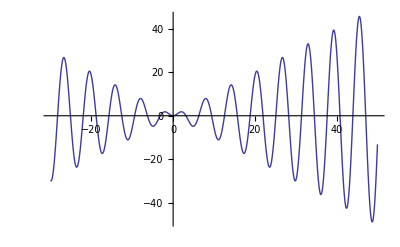

```mathematica
f[x_]:=x Sin[x]
Plot[f[x],{x,-30,50}]
```

```mathematica
fitRate=0.4;
{xmin,xmax}={-30,50};
populationNum=50;
fitpopulationNum=Floor[fitRate*populationNum];
population=RandomInteger[{1,2^22},populationNum];
itermax=5000;
pic=Plot[f[x],{x,xmin,xmax}];
Dynamic[Show[{pic,ListPlot[SortBy[({N[((xmax-xmin)#)/2^22+xmin],N@f[((xmax-xmin)#)/2^22+xmin]})&/@population,-#[[2]]&],PlotMarkers->Automatic]},PlotLabel->itermax]]
While[itermax>0,
valueOfx=SortBy[({#,N@f[((xmax-xmin)#)/2^22+xmin]})&/@population,-#[[2]]&];
fitx=valueOfx[[1;;fitpopulationNum,1]];
generateNum=5;
crossx=Flatten[(CrossGenetic[#[[1]],#[[2]],codeLength,generateNum])&/@RandomChoice[fitx,{Floor[fitpopulationNum],2}]];
aberrancex=aberranceGenetic[#,codeLength]&/@fitx;
itermax--;
population=Join[crossx,aberrancex,fitx];
]
```

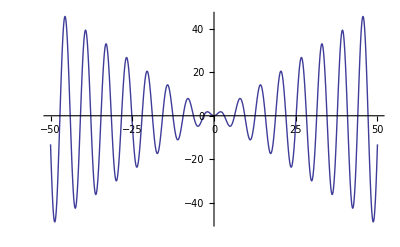

```mathematica
Plot[f[x],{x,-50,50}]
```